# Phase Boundary Calculations

```mathematica
ClearAll["Global`*"];
```

## Exact Hamiltonian

### Eigenstates

```mathematica
(* Ground-states and first excited states *)
plusState[a1_,a2_,a4_,a5_]:={0,0,a4,0,0,-a1,0,0,a2,0,0,-a5,0}
minusState[a1_,a2_,a4_,a5_]:={0,a5,0,0,a2,0,0,a1,0,0,a4,0,0}
upState[b1_,b2_,b4_,b5_]:={0,0,b4,0,0,b1,0,0,b2,0,0,b5,0}
downState[b1_,b2_,b4_,b5_]:={0,-b5,0,0,b2,0,0,-b1,0,0,b4,0,0}

a1=0.0960023006569961009317604323639708844716307460964755250591787622584529813089767698810571800909907200936626013310387`100.;
a2=0.1388976829934512769899363793643009436431045855160542453041384163665907376155181566008226602983001450395344287920164`100.;
a4=0.9402137436584117102803389171690795195304604179630104367516510172338664876161921960814106181068536878355883513006478`100.;
a5=-0.2957855780180110731489345119842823279986769978294281290514432539519923893431000063944642632227447313723561228891602`100.;
b1=0.08090317125160954513715635470348177155953048715735091092074244352876699682114508866445549236451570901970918703058`100.;
b2=0.191700815055299746877764249022576091859205866633585219188354308845149831841360096334160179449731245038678965028986`100.;
b4=-0.3117226472320488193286928449592719544221997281340119030578105816066006378278671108417326679997032775713005252249615`100.;
b5=0.9271108162410846058075149011383053038963114115323363041768748809065148838751133789071431892027360344146560344223858`100.;

states={plusState[a1,a2,a4,a5],minusState[a1,a2,a4,a5],upState[b1,b2,b4,b5],downState[b1,b2,b4,b5]};
```

### Position Conventions

```mathematica
(* Position conventions for atoms in the tetrahedron using Curnoe *)
r1={1,1,1}/(2*√2);
r2={-1,-1,1}/(2*√2);
r3={-1,1,-1}/(2*√2);
r4={1,-1,-1}/(2*√2);

(* Position conventions for atoms in the tetrahedron using Ross *)
(*r1={1,1,1}/(2*√2);
r2={1,-1,-1}/(2*√2);
r3={-1,1,-1}/(2*√2);
r4={-1,-1,1}/(2*√2);*)

r={r1,r2,r3,r4};
```

### Local Bases Conventions

```mathematica
(* Rotation matrices changing from global to local axes using Curnoe *)
u1=1/√6*{{1,-√3,√2},
		{1,√3,√2},
		{-2,0,√2}};
u2=1/√6*{{-1,√3,-√2},
		{-1,-√3,-√2},
		{-2,0,√2}};
u3=1/√6*{{-1,√3,-√2},
		{1,√3,√2},
		{2,0,-√2}};
u4=1/√6*{{1,-√3,√2},
		{-1,-√3,-√2},
		{2,0,-√2}};

(* Rotation matrices changing from global to local axes using Ross *)
(*u1=1/√6*{{-2,0,√2},
		{1,-√3,√2},
		{1,√3,√2}};
u2=1/√6*{{-2,0,√2},
		{-1,√3,-√2},
		{-1,-√3,-√2}};
u3=1/√6*{{2,0,-√2},
		{1,-√3,√2},
		{-1,-√3,-√2}};
u4=1/√6*{{2,0,-√2},
		{-1,√3,-√2},
		{1,√3,√2}};*)

u={u1,u2,u3,u4};
```

### Angular Momentum Operators

```mathematica
(* (2J + 1)×(2J + 1) representation of angular momentum operators used for exact diagonalization within the ground-state/first-excited state manifold on a single tetrahedron *)
J=6;
Jz=DiagonalMatrix[Range[-6,6]];
Jm=ConstantArray[0,{2*J+1,2*J+1}];
Do[
	Jm⟦m+(J+1),m+1+(J+1)⟧=Sqrt[(J*(J+1)-m*(m+1))];,{m,-J,J-1}
];
Jp=Jm†;
Jx=1/2*(Jp+Jm);
Jy=1/(2*I)*(Jp-Jm);

id=IdentityMatrix[4];
zero=ConstantArray[0,{4,4}];

(* 4^4 × 4^4 = 256 × 256 representation of angular momentum operators for the four different atoms in a tetrahedron *)
JxList[states_]:=Module[{matrix,J1x,J2x,J3x,J4x,list},
matrix=zero;
Do[
matrix⟦i,j⟧=states⟦i⟧.Jx.states⟦j⟧;,{i,4},{j,4}
];
J1x=SparseArray[KroneckerProduct[matrix,id,id,id]];
J2x=SparseArray[KroneckerProduct[id,matrix,id,id]];
J3x=SparseArray[KroneckerProduct[id,id,matrix,id]];
J4x=SparseArray[KroneckerProduct[id,id,id,matrix]];
list={J1x,J2x,J3x,J4x};
list
];

JyList[states_]:=Module[{matrix,J1y,J2y,J3y,J4y,list},
matrix=zero;
Do[
matrix⟦i,j⟧=states⟦i⟧.Jy.states⟦j⟧;,{i,4},{j,4}
];
J1y=SparseArray[KroneckerProduct[matrix,id,id,id]];
J2y=SparseArray[KroneckerProduct[id,matrix,id,id]];
J3y=SparseArray[KroneckerProduct[id,id,matrix,id]];
J4y=SparseArray[KroneckerProduct[id,id,id,matrix]];
list={J1y,J2y,J3y,J4y};
list
];

JzList[states_]:=Module[{matrix,J1z,J2z,J3z,J4z,list},
matrix=zero;
Do[
matrix⟦i,j⟧=states⟦i⟧.Jz.states⟦j⟧;,{i,4},{j,4}
];
J1z=SparseArray[KroneckerProduct[matrix,id,id,id]];
J2z=SparseArray[KroneckerProduct[id,matrix,id,id]];
J3z=SparseArray[KroneckerProduct[id,id,matrix,id]];
J4z=SparseArray[KroneckerProduct[id,id,id,matrix]];
list={J1z,J2z,J3z,J4z};
list
];

Js=Transpose[{JxList[states],
JyList[states],
JzList[states]}];
```

### Crystal Field Hamiltonian (H_cf)

```mathematica
(* Crystal field Hamiltonians on a single tetrahedra *)
Hcf[Δ_]:=DiagonalMatrix[{0,0,Δ,Δ}];

Hcf1[Δ_]:=KroneckerProduct[Hcf[Δ],id,id,id];
Hcf2[Δ_]:=KroneckerProduct[id,Hcf[Δ],id,id];
Hcf3[Δ_]:=KroneckerProduct[id,id,Hcf[Δ],id];
Hcf4[Δ_]:=KroneckerProduct[id,id,id,Hcf[Δ]];
HcfFull[Δ_]:=Hcf1[Δ]+Hcf2[Δ]+Hcf3[Δ]+Hcf4[Δ];
```

### Interaction Hamiltonian (H_int = H_ex + H_d)

```mathematica
(* Coupling constant *)
F[i_,j_,α_,β_,𝒥_,𝒟_]:=𝒥*KroneckerDelta[α,β]+𝒟*(KroneckerDelta[α,β]-3*(r⟦j,α⟧-r⟦i,α⟧)*(r⟦j,β⟧-r⟦i,β⟧));

(* Interaction Hamiltonian *)
(* Note that Subscript[J, iα] in the global frame is given by ∑_β Subscript[u, i,αβ] Subscript[J, i]^β in the local frame *)
Hint[𝒥_,𝒟_]:=Sum[F[i,j,α1,β1,𝒥,𝒟]*u⟦i,α1,α2⟧*u⟦j,β1,β2⟧*Js⟦i,α2⟧.Js⟦j,β2⟧,{i,3},{j,i+1,4},{α1,3},{α2,3},{β1,3},{β2,3}];
```

### Determination of 𝒥_c

```mathematica
(* 1/Δ points *)
InverseΔList={0.000046656298600308496,0.0009331259720062202,0.0019595645412130644,0.0033125972006220836,0.004992223950233283,0.0066718506998444775,0.009984447900466563,0.01250388802488336,0.015,0.01665629860031104,0.0175,0.020808709175738727,0.0225,0.025007776049766724,0.0275,0.028506998444790047,0.03,0.0325,0.03331259720062209,0.035,0.0375,0.03998444790046657,0.0425,0.04544323483670297,0.0475,0.05,0.05351477449455676};
ΔList=1./InverseΔList;

(* Critical 𝒥 points signifying the change in ground-state degeneracy (change of phase) *)
λList={0.0};
𝒥cList=Table[0,{i,Length[λList]},{j,Length[ΔList]}];

𝒟=0.0315;

startTime=AbsoluteTime[];

For[i=1,i≤Length[λList],i++,
λ=λList⟦i⟧;

(* Binary search to determine Subscript[𝒥, c] phase-boundary between the singlet and non-singlet states for H = Subscript[H, cf] + Subscript[H, ex]+ Subscript[H, d] *)
For[j=1,j≤Length[ΔList],j++,
Δ=ΔList⟦j⟧;
a=-2.0;
b=2.0;

crystalFieldH=HcfFull[Δ];

HA=crystalFieldH+Hint[a,𝒟];
energiesA=Sort[Chop[Eigenvalues[HA]]];
minEnergyA=Min[energiesA];
degeneracyA=Length[Select[energiesA-minEnergyA,#<0.00001&]];

HB=crystalFieldH+Hint[b,𝒟];
energiesB=Sort[Chop[Eigenvalues[HB]]];
minEnergyB=Min[energiesB];
degeneracyB=Length[Select[energiesB-minEnergyB,#<0.00001&]];

While[Abs[b-a]≥0.000001,
c=(a+b)/2;
HC=crystalFieldH+Hint[c,𝒟];
energiesC=Sort[Chop[Eigenvalues[HC]]];
minEnergyC=Min[energiesC];
degeneracyC=Length[Select[energiesC-minEnergyC,#<0.00001&]];

If[degeneracyC==1,a=c,b=c];
];
𝒥cList⟦i,j⟧=c;
]
]
Print[AbsoluteTime[]-startTime];

𝒥c2List=Table[0,{i,Length[λList]},{j,Length[ΔList]}];

For[i=1,i≤Length[λList],i++,
λ=λList⟦i⟧;

(* Binary search to determine Subscript[𝒥, c] phase-boundary between the doublet and non-doublet states for H = Subscript[H, cf] + Subscript[H, ex]+ Subscript[H, d] *)
For[j=1,j≤Length[ΔList],j++,
Δ=ΔList⟦j⟧;
a=-2.0;
b=2.0;

crystalFieldH=HcfFull[Δ];

HA=crystalFieldH+Hint[a,𝒟];
energiesA=Sort[Chop[Eigenvalues[HA]]];
minEnergyA=Min[energiesA];
degeneracyA=Length[Select[energiesA-minEnergyA,#<0.000001&]];

HB=crystalFieldH+Hint[b,𝒟];
energiesB=Sort[Chop[Eigenvalues[HB]]];
minEnergyB=Min[energiesB];
degeneracyB=Length[Select[energiesB-minEnergyB,#<0.000001&]];

While[Abs[b-a]≥0.00001,
c=(a+b)/2;
HC=crystalFieldH+Hint[c,𝒟];
energiesC=Sort[Chop[Eigenvalues[HC]]];
minEnergyC=Min[energiesC];
degeneracyC=Length[Select[energiesC-minEnergyC,#<0.000001&]];

If[degeneracyC==2,b=c,a=c];
];
𝒥c2List⟦i,j⟧=c;
]
]
Print[AbsoluteTime[]-startTime];
```

177.093449

331.949596

### Phase Boundary Plot

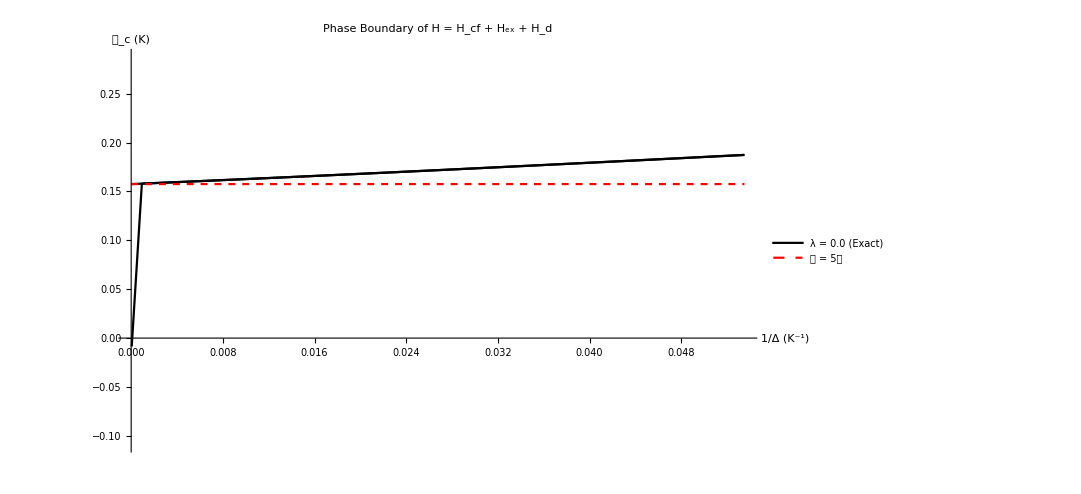

```mathematica
(* Phase boundary plots *)
maxX=Max[InverseΔList];
minY=Min[𝒥cList]-0.1;
maxY=Max[𝒥cList]+0.1;
data=ConstantArray[0,Length[λList]];
plot=ConstantArray[0,Length[λList]];
For[i=1,i≤Length[λList],i++,
data⟦i⟧=Transpose[{InverseΔList,𝒥cList⟦i⟧}];
plot⟦i⟧=ListPlot[data⟦i⟧,Joined->True,PlotRange->{{0,maxX},{minY,maxY}},PlotStyle->ColorData[3,i],PlotLegends->{"λ = "<>ToString[NumberForm[λList⟦i⟧,{1,1}]]<>" (Exact)"}];
]
data2=ConstantArray[0,Length[λList]];
plot2=ConstantArray[0,Length[λList]];
For[i=1,i≤Length[λList],i++,
data2⟦i⟧=Transpose[{InverseΔList,𝒥c2List⟦i⟧}];
plot2⟦i⟧=ListPlot[data2⟦i⟧,Joined->True,PlotRange->{{0,maxX},{minY,maxY}},PlotStyle->ColorData[3,i]];
]

horizontalLine=Plot[𝒥c2List⟦1,1⟧,{x,0,maxX},PlotStyle->{Red,Dashed},PlotLegends->{"𝒥 = 5𝒟"}];

Show[Flatten[{plot,plot2,horizontalLine}],PlotLabel->"Phase Boundary of H = H_cf + H_ex + H_d",AxesLabel->{"1/Δ (K^-1)","𝒥_c (K)"},ImageSize->800,LabelStyle->{FontSize->20}]
```

### State Determination

```mathematica
(* Determine which basis state the ground states form *)
```

```mathematica
(* Eigenstates represented in the basis of the two lowest-lying doublets *)
pState={1,0,0,0};
mState={0,1,0,0};

mmmm=Flatten[KroneckerProduct[mState,mState,mState,mState]];

pmmm=Flatten[KroneckerProduct[pState,mState,mState,mState]];
mpmm=Flatten[KroneckerProduct[mState,pState,mState,mState]];
mmpm=Flatten[KroneckerProduct[mState,mState,pState,mState]];
mmmp=Flatten[KroneckerProduct[mState,mState,mState,pState]];

ppmm=Flatten[KroneckerProduct[pState,pState,mState,mState]];
pmpm=Flatten[KroneckerProduct[pState,mState,pState,mState]];
pmmp=Flatten[KroneckerProduct[pState,mState,mState,pState]];
mppm=Flatten[KroneckerProduct[mState,pState,pState,mState]];
mpmp=Flatten[KroneckerProduct[mState,pState,mState,pState]];
mmpp=Flatten[KroneckerProduct[mState,mState,pState,pState]];

pppm=Flatten[KroneckerProduct[pState,pState,pState,mState]];
ppmp=Flatten[KroneckerProduct[pState,pState,mState,pState]];
pmpp=Flatten[KroneckerProduct[pState,mState,pState,pState]];
mppp=Flatten[KroneckerProduct[mState,pState,pState,pState]];

pppp=Flatten[KroneckerProduct[pState,pState,pState,pState]];

ϵ=Exp[2*π*ⅈ/3]//N;

(* Tetrahedron basis states given by "Quantum spin configurations in Tb_2Ti_2O_7" by Curnoe, doi:10.1103/PhysRevB.75.212404 *)
A1=1/√6*(ppmm+pmpm+pmmp+mppm+mpmp+mmpp);
Ep1=pppp;
Em1=mmmm;
Ep2=1/2*(pmmm+mpmm+mmpm+mmmp);
Em2=1/2*(pppm+ppmp+pmpp+mppp);
Ep3=1/√6*(ppmm+ϵ*pmpm+ϵ^2*pmmp+mmpp+ϵ*mpmp+ϵ^2*mppm);
Em3=1/√6*(ppmm+ϵ**pmpm+ϵ*^2*pmmp+mmpp+ϵ**mpmp+ϵ*^2*mppm);
T1x1=1/(2*√2)*(-ϵ^2*pppm+ϵ^2*ppmp+ϵ^2*pmpp-ϵ^2*mppp+ϵ*pmmm-ϵ*mpmm-ϵ*mmpm+ϵ*mmmp);
T1y1=1/(2*√2)*(ϵ*pppm-ϵ*ppmp+ϵ*pmpp-ϵ*mppp+ϵ^2*pmmm-ϵ^2*mpmm+ϵ^2*mmpm-ϵ^2*mmmp);
T1z1=1/(2*√2)*(pppm+ppmp-pmpp-mppp+pmmm+mpmm-mmpm-mmmp);
T1x2=1/√2*(pmmp-mppm);
T1y2=1/√2*(pmpm-mpmp);
T1z2=1/√2*(ppmm-mmpp);
T2x=1/(2*√2)*(-ϵ^2*pppm+ϵ^2*ppmp+ϵ^2*pmpp-ϵ^2*mppp-ϵ*pmmm+ϵ*mpmm+ϵ*mmpm-ϵ*mmmp);
T2y=1/(2*√2)*(ϵ*pppm-ϵ*ppmp+ϵ*pmpp-ϵ*mppp-ϵ^2*pmmm+ϵ^2*mpmm-ϵ^2*mmpm+ϵ^2*mmmp);
T2z=1/(2*√2)*(pppm+ppmp-pmpp-mppp-pmmm-mpmm+mmpm+mmmp);
```

```mathematica
(* 1/Δ points *)
InverseΔList={0.000046656298600308496,0.0009331259720062202,0.0019595645412130644,0.0033125972006220836,0.004992223950233283,0.0066718506998444775,0.009984447900466563,0.01250388802488336,0.015,0.01665629860031104,0.0175,0.020808709175738727,0.0225,0.025007776049766724,0.0275,0.028506998444790047,0.03,0.0325,0.03331259720062209,0.035,0.0375,0.03998444790046657,0.0425,0.04544323483670297,0.0475,0.05,0.05351477449455676};
ΔList=1./InverseΔList;

(* Critical 𝒥 points signifying the change in ground-state degeneracy (change of phase) *)
λList={0.0};
ΔList={100};
𝒥List=Range[-2,2,0.01];
fidelityList=Table[0,{n,16},{i,Length[λList]},{j,Length[ΔList]},{k,Length[𝒥List]}];

For[i=1,i≤Length[λList],i++,
λ=λList⟦i⟧;

For[j=1,j≤Length[ΔList],j++,
Δ=ΔList⟦j⟧;
crystalFieldH=HcfFull[Δ];

For[k=1,k≤Length[𝒥List],k++,
𝒥=𝒥List⟦k⟧;

H=crystalFieldH+Hint[𝒥,𝒟];
{energies,energyKets}=Transpose[Sort[Transpose[Eigensystem[H]],Re[#1⟦1⟧]<Re[#2⟦1⟧]&]];
energies=Take[energies,16];
energyKets=Take[Chop[energyKets,10^-6],16];
fidelityList⟦1,i,j,k⟧=Norm[energyKets⟦1⟧.A1]//Chop;
fidelityList⟦2,i,j,k⟧=Norm[energyKets⟦1⟧.Ep3]//Chop;
fidelityList⟦3,i,j,k⟧=Norm[energyKets⟦1⟧.Em3]//Chop;
fidelityList⟦4,i,j,k⟧=Norm[energyKets⟦1⟧.T1x2]//Chop;
fidelityList⟦5,i,j,k⟧=Norm[energyKets⟦1⟧.T1y2]//Chop;
fidelityList⟦6,i,j,k⟧=Norm[energyKets⟦1⟧.T1z2]//Chop;
fidelityList⟦7,i,j,k⟧=Norm[energyKets⟦1⟧.Ep1]//Chop;
fidelityList⟦8,i,j,k⟧=Norm[energyKets⟦1⟧.Em1]//Chop;
]
]
]
```

### Fidelity Plots

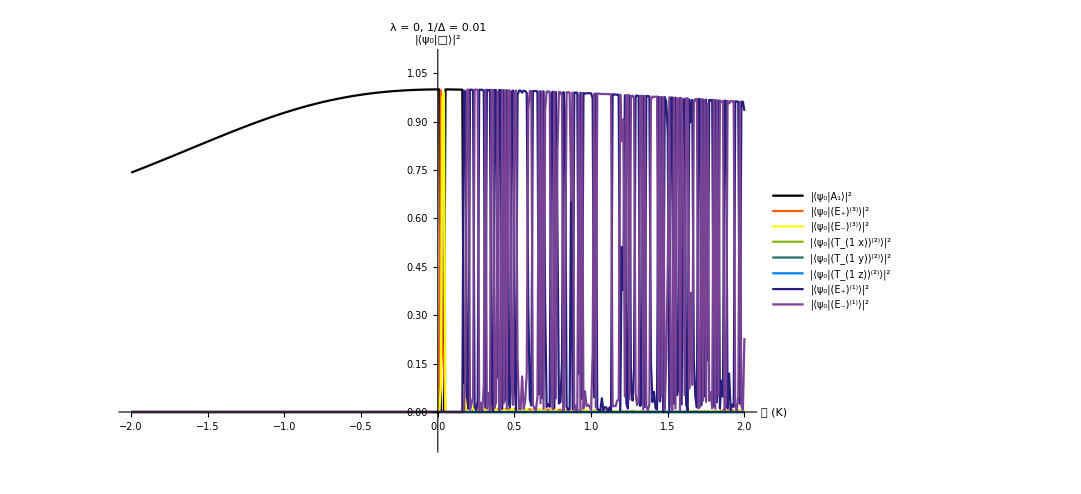

```mathematica
(* Phase boundary plots *)
minX=Min[𝒥List];
maxX=Max[𝒥List];
minY=Min[fidelityList]-0.1;
maxY=Max[fidelityList]+0.1;
data=ConstantArray[0,8];
plot=ConstantArray[0,8];

legend= {"A_1","(E_+)^(3)","(E_-)^(3)","(T_(1  x))^(2)","(T_(1  y))^(2)","(T_(1  z))^(2)","(E_+)^(1)","(E_-)^(1)"};
For[n=1,n≤8,n++,
data⟦n⟧=Transpose[{𝒥List,fidelityList⟦n,1,1,All⟧}];
plot⟦n⟧=ListPlot[data⟦n⟧,Joined->True,PlotRange->{{minX,maxX},{minY,maxY}},PlotStyle->ColorData[3,n],PlotLegends->{"|⟨ψ_0|"<>legend⟦n⟧<>"⟩|^2"}];
]

Show[plot,PlotLabel->"λ = 0, 1/Δ = 0.01",AxesLabel->{"𝒥 (K)","|⟨ψ_0|□⟩|^2"},ImageSize->800,LabelStyle->{FontSize->20}]
```

## Effective Hamiltonian

### Eigenstates

```mathematica
(* Ground-states and first excited states *)
plusState[a1_,a2_,a4_,a5_]:={0,0,a4,0,0,-a1,0,0,a2,0,0,-a5,0}
minusState[a1_,a2_,a4_,a5_]:={0,a5,0,0,a2,0,0,a1,0,0,a4,0,0}
upState[b1_,b2_,b4_,b5_]:={0,0,b4,0,0,b1,0,0,b2,0,0,b5,0}
downState[b1_,b2_,b4_,b5_]:={0,-b5,0,0,b2,0,0,-b1,0,0,b4,0,0}

a1=0.0960023006569961009317604323639708844716307460964755250591787622584529813089767698810571800909907200936626013310387`100.;
a2=0.1388976829934512769899363793643009436431045855160542453041384163665907376155181566008226602983001450395344287920164`100.;
a4=0.9402137436584117102803389171690795195304604179630104367516510172338664876161921960814106181068536878355883513006478`100.;
a5=-0.2957855780180110731489345119842823279986769978294281290514432539519923893431000063944642632227447313723561228891602`100.;
b1=0.08090317125160954513715635470348177155953048715735091092074244352876699682114508866445549236451570901970918703058`100.;
b2=0.191700815055299746877764249022576091859205866633585219188354308845149831841360096334160179449731245038678965028986`100.;
b4=-0.3117226472320488193286928449592719544221997281340119030578105816066006378278671108417326679997032775713005252249615`100.;
b5=0.9271108162410846058075149011383053038963114115323363041768748809065148838751133789071431892027360344146560344223858`100.;

states={plusState[a1,a2,a4,a5],minusState[a1,a2,a4,a5],upState[b1,b2,b4,b5],downState[b1,b2,b4,b5]};
```

### Phase Factors Conventions

```mathematica
(* Defining the phase factors Subscript[Λ, ij] following conventions by Mukherjee and Curnoe *)
lambda={{0,1,-1/2+√3/2*I,-1/2-√3/2*I},
{1,0,-1/2-√3/2*I,-1/2+√3/2*I},
{-1/2+√3/2*I,-1/2-√3/2*I,0,1},
{-1/2-√3/2*I,-1/2+√3/2*I,1,0}};

(* Defining the phase factors Subscript[Λ, ij] following conventions by Ross et al. *)
(*lambda={{0,1,-1/2-√3/2*I,-1/2+√3/2*I},
		{1,0,-1/2+√3/2*I,-1/2-√3/2*I},
		{-1/2-√3/2*I,-1/2+√3/2*I,0,1},
		{-1/2+√3/2*I,-1/2-√3/2*I,1,0}};*)
```

### Angular Momentum Operators

```mathematica
(* Angular momentum operators *)
J=6;
Jz=DiagonalMatrix[Range[-6,6]];
Jm=ConstantArray[0,{2*J+1,2*J+1}];
Do[
	Jm⟦m+(J+1),m+1+(J+1)⟧=Sqrt[(J*(J+1)-m*(m+1))];,{m,-J,J-1}
];
Jp=Jm†;
Jx=1/2*(Jp+Jm);
Jy=1/(2*I)*(Jp-Jm);
id=IdentityMatrix[2*J+1];

(* Stevens operators *)
X=J*(J+1);
O2n2=Jx.Jy+Jy.Jx;
O2n1=1/2*(Jy.Jz+Jz.Jy);
O20=3*Jz.Jz-X*id;
O21=1/2*(Jx.Jz+Jz.Jx);
O22=Jx.Jx-Jy.Jy;

(* Pseudospin-1/2 matrices *)
sz={{1,0},{0,-1}};
sp={{0,1},{0,0}};
sm={{0,0},{1,0}};
id=IdentityMatrix[2];

(* Lists of 2^4 × 2^4 = 16 × 16 representation of the pseudospin-1/2 operators for atom sites 1, 2, 3, and 4 on a single tetrahedron *)
s1z=KroneckerProduct[sz,id,id,id];
s2z=KroneckerProduct[id,sz,id,id];
s3z=KroneckerProduct[id,id,sz,id];
s4z=KroneckerProduct[id,id,id,sz];

s1p=KroneckerProduct[sp,id,id,id];
s2p=KroneckerProduct[id,sp,id,id];
s3p=KroneckerProduct[id,id,sp,id];
s4p=KroneckerProduct[id,id,id,sp];

s1m=KroneckerProduct[sm,id,id,id];
s2m=KroneckerProduct[id,sm,id,id];
s3m=KroneckerProduct[id,id,sm,id];
s4m=KroneckerProduct[id,id,id,sm];

szList={s1z,s2z,s3z,s4z};
spList={s1p,s2p,s3p,s4p};
smList={s1m,s2m,s3m,s4m};

idFull=IdentityMatrix[16];
zeroFull=ConstantArray[0,{16,16}];
```

### Matrix Elements

```mathematica
(* Matrix elements *)
matrixElements[states_]:=Module[{p,m,u,d,j1,j2,j3,j4,j5,j6,j7,j8,j9,t,matrixElementsList},
p=states⟦1⟧;
m=states⟦2⟧;
u=states⟦3⟧;
d=states⟦4⟧;

j1=p.Jz.p;
j2=u.Jz.u;
j3=u.Jz.p;
t=u.Jp.m;
j4=p.O2n2.m/ⅈ;
j5=u.O2n2.m/ⅈ;
j6=p.O2n1.m/ⅈ;
j7=u.O2n1.m/ⅈ;
j8=p.O20.p;
j9=u.O20.p;

matrixElementsList={j1,j2,j3,j4,j5,j6,j7,j8,j9,t};
matrixElementsList
];
```

### Coupling Constants

```mathematica
couplings[matrixElementsList_,Δ_,𝒥_,𝒟_,𝒬_]:=Module[{j1,j2,j3,j4,j5,j6,j7,j8,j9,t,I1,I2,I3,I4,const,jzz,jpm,jpp,jzp,jzpz,jppp,jppm,couplingConstants},
(* {Subscript[j, 1], Subscript[j, 2], Subscript[j, 3], Subscript[j, 4], Subscript[j, 5], Subscript[j, 6], Subscript[j, 7], Subscript[j, 8], Subscript[j, 9], t} *)
j1=matrixElementsList⟦1⟧;
j2=matrixElementsList⟦2⟧;
j3=matrixElementsList⟦3⟧;
j4=matrixElementsList⟦4⟧;
j5=matrixElementsList⟦5⟧;
j6=matrixElementsList⟦6⟧;
j7=matrixElementsList⟦7⟧;
j8=matrixElementsList⟦8⟧;
j9=matrixElementsList⟦9⟧;
t=matrixElementsList⟦10⟧;

I1=𝒥-5*𝒟;
I2=𝒥-1/2*𝒟;
I3=𝒥+7/4*𝒟;
I4=𝒥-1/2*𝒟;

const=0;
jzz=0;
jpm=0;
jpp=0;
jzp=0;
jzpz=0;
jppp=0;
jppm=0;

(* Couplings from Subscript[PH, ex] P *)
jzz+=-1/3*I1*j1^2;

(* Couplings from Subscript[PH, ex] Subscript[QH, ex] P *)
const+=(-1/Δ)*(4*I1^2*j1^2*j3^2/3+8*I2^2*j1^2*t^2/3+I1^2*j3^4/3+4*I2^2*j3^2*t^2/3+I3^2*t^4/6+I4^2*t^4/24);
jzz+=(-1/Δ)*(4*I1^2*j1^2*j3^2/9-4*I2^2*j1^2*t^2/9+I3^2*t^4/36-I4^2*t^4/144);
jpm+=(-1/Δ)*(I1*I4*j3^2*t^2/18+2*I2^2*j3^2*t^2/9);
jpp+=(-1/Δ)*(-I1*I3*j3^2*t^2/9+2*I2^2*j3^2*t^2/9);
jzpz+=(-1/Δ)*(2*√2*I1*I2*j1^2*j3*t/9);

(* Couplings from Subscript[PH, EQQ] P *)
const+=51/4*𝒬*j8^2;
jpm+=1/8*𝒬*(j4^2-104*√2*j4*j6+80*j6^2);
jpp+=1/8*𝒬*(49*j4^2-8*√2*j4*j6+368*j6^2);

(* Couplings from Subscript[PH, ex] Subscript[QH, eqq] P and its Hermitian conjugate *)
(* Subscript[PX, 1] Subscript[Q, o] Subscript[H, EQQ] P *)
jzz+=(-1/Δ)*𝒬*(-17/2)*I1*j1*j3*j8*j9;
jpm+=(-1/Δ)*𝒬*I1*j1*j3*(j4*j5/6-26*√2*j5*j6/3-26*√2*j4*j7/3+40*j6*j7/3) ;
jpp+=(-1/Δ)*𝒬*I1*j1*j3*(-49*j4*j5/6+2*√2*j5*j6/3+2*√2*j4*j7/3-184*j6*j7/3);
jzpz+=(-1/Δ)*𝒬*I1*j1*j3*(j4/4+√2*j6)*j9;

(* Subscript[PX, 2] Subscript[Q, o] Subscript[H, EQQ] P *)
jpm+=(-1/Δ)*𝒬*I2*j1*(√2*j4/2+4*j6)*j9*t;
jpp+=(-1/Δ)*𝒬*I2*j1*(-√2*j4/2-4*j6)*j9*t;
jzpz+=(-1/Δ)*𝒬*I2*j1*t*(47*√2*j4*j5/24+25*j5*j6/3+25*j4*j7/3+26*√2*j6*j7/3);

(* Subscript[PX, 3] Subscript[Q, o] Subscript[H, EQQ] P *)
(* No contributions to coupling constants *)

(* Subscript[PX, 4] Subscript[Q, o] Subscript[H, EQQ] P *)
(* No contributions to coupling constants *)

(* Subscript[PX, 1] Subscript[Q, t] Subscript[H, EQQ] P *)
jzz+=(-1/(2*Δ))*𝒬*(-17/12)*I1*j3^2*j9^2;
jpm+=(-1/(2*Δ))*𝒬*I1*j3^2*(j5^2-104*√2*j5*j7+80*j7^2)/12;
jpp+=(-1/(2*Δ))*𝒬*I1*j3^2* (-49*j5^2+8 √2*j5*j7-368*j7^2)/12;

(* Subscript[PX, 2] Subscript[Q, t] Subscript[H, EQQ] P *)
jzz+=(-1/(2*Δ))*𝒬*I2*j3*(-√2*j5-8*j7)*j9*t/2;
jpm+=(-1/(2*Δ))*𝒬*I2*j3*(√2*j5+8*j7)*j9*t/2;
jpp+=(-1/(2*Δ))*𝒬*I2*j3*(-√2*j5-8*j7)*j9*t/2;

(* Subscript[PX, 3] Subscript[Q, t] Subscript[H, EQQ] P *)
const+=(-1/(2*Δ))*𝒬*I3*(49*j5^2-8*√2*j5*j7+368*j7^2)/4*t^2;
jzz+=(-1/(2*Δ))*𝒬*I3*(49*j5^2-8*√2*j5*j7+368*j7^2)/24*t^2;
jpp+=(-1/(2*Δ))*𝒬*17/12*I3*j9^2*t^2;

(* Subscript[PX, 4] Subscript[Q, t] Subscript[H, EQQ] P *)
const+=(-1/(2*Δ))*𝒬*I4*(j5^2-104*√2*j5*j7+80*j7^2)/8*t^2;
jzz+=(-1/(2*Δ))*𝒬*I4*(-j5^2+104*√2*j5*j7-80*j7^2)/48*t^2;
jpm+=(-1/(2*Δ))*𝒬*(17/24)*I4*j9^2*t^2;

(* CHECK *)
(* Subscript[PH, EQQ] Subscript[Q, o] Subscript[H, EQQ] P *)
const+=-1/(16 Δ)3 (1201 j4^2 j5^2-248 √2 j4 j5^2 j6+2720 j5^2 j6^2-248 √2 j4^2 j5 j7+23552 j4 j5 j6 j7-5632 √2 j5 j6^2 j7+2720 j4^2 j7^2-5632 √2 j4 j6 j7^2+70912 j6^2 j7^2+9 j4^2 j9^2+72 √2 j4 j6 j9^2+288 j6^2 j9^2+867 j8^2 j9^2) 𝒬^2;
jzz+=-1/(4 Δ)3 (25 j4^2 j5^2-3 √2 j4 j5^2 j6-56 j5^2 j6^2+25 j4^2 j5 j7+22 √2 j4^2 j5 j7+356 j4 j5 j6 j7-3 √2 j4 j5 j6 j7-56 j5 j6^2 j7-112 √2 j5 j6^2 j7-112 j4^2 j7^2-28 √2 j4^2 j7^2+168 j4 j6 j7^2+112 √2 j4 j6 j7^2+2688 j6^2 j7^2+224 √2 j6^2 j7^2) 𝒬^2;
jpm+=1/(64 Δ)(2399 j4^2 j5^2-184 √2 j4 j5^2 j6-10784 j5^2 j6^2-184 √2 j4^2 j5 j7+14176 j4 j5 j6 j7+13696 √2 j5 j6^2 j7-10784 j4^2 j7^2+13696 √2 j4 j6 j7^2+122624 j6^2 j7^2-204 j4 j5 j8 j9+10608 √2 j5 j6 j8 j9+10608 √2 j4 j7 j8 j9-16320 j6 j7 j8 j9+18 j4^2 j9^2+144 √2 j4 j6 j9^2+576 j6^2 j9^2) 𝒬^2 ;
jpp+=1/(32 Δ)(49 j4^2 j5^2-2552 √2 j4 j5^2 j6+416 j5^2 j6^2-2552 √2 j4^2 j5 j7+5120 j4 j5 j6 j7-19456 √2 j5 j6^2 j7+416 j4^2 j7^2-19456 √2 j4 j6 j7^2+29440 j6^2 j7^2-4998 j4 j5 j8 j9+408 √2 j5 j6 j8 j9+408 √2 j4 j7 j8 j9-37536 j6 j7 j8 j9-18 j4^2 j9^2-144 √2 j4 j6 j9^2-576 j6^2 j9^2) 𝒬^2;
jppp+=-(9 (49 j4^2 j5+192 √2 j4 j5 j6-32 j5 j6^2-4 √2 j4^2 j7+336 j4 j6 j7+1472 √2 j6^2 j7) j9 𝒬^2)/(32 Δ);
jppm+=-(9 (j4^2 j5+5 √2 j4 j5 j6+8 j5 j6^2+√2 j4^2 j7+14 j4 j6 j7+24 √2 j6^2 j7) j9 𝒬^2)/(2 Δ);

(* {C, Subscript[J, zz], J_(±∓), J_(±±), J_(z±), Subscript[J, z±z], J_(±±±), J_(±±∓)} *)
couplingConstants={const,jzz,jpm,jpp,jzp,jzpz,jppp,jppm};
couplingConstants
];
```

### Projected Hamiltonian

```mathematica
(* Defining the different possible components of the projected Hamiltonian along with their coupling strengths *)
```

```mathematica
(* 16 × 16 representation of the Hamiltonian in units of meV given values for Δ, 𝒥, 𝒟, and 𝒬 in units of Kelvin (K), as well as the four states *)
projectedHamiltonian[Δ_Real|Δ_Integer,𝒥_Real|𝒥_Integer,𝒟_Real|𝒟_Integer,𝒬_Real|𝒬_Integer,states_]:=Module[{matrixElementsList,couplingConstants,const,jzz,jpm,jpp,jzp,jzpz,jppp,jppm,Hzz,Hpm,Hpp,Hzp,Hzpz,Hppp,Hppm,totalH},
matrixElementsList=matrixElements[states];
couplingConstants=couplings[matrixElementsList,Δ,𝒥,𝒟,𝒬];

(* {C, Subscript[J, zz], J_(±∓), J_(±±), J_(z±), Subscript[J, z±z], J_(±±±), J_(±±∓)} *)
const=couplingConstants⟦1⟧;
jzz=couplingConstants⟦2⟧;
jpm=couplingConstants⟦3⟧;
jpp=couplingConstants⟦4⟧;
jzp=couplingConstants⟦5⟧;
jzpz=couplingConstants⟦6⟧;
jppp=couplingConstants⟦7⟧;
jppm=couplingConstants⟦8⟧;

Hzpz=zeroFull;

(* ∑_⟨i,j⟩ (Subscript[σ, iz] Subscript[σ, jz]) *)
Hzz=Sum[szList⟦i⟧.szList⟦j⟧,{i,3},{j,i+1,4}];

(* ∑_⟨i,j⟩ (σ_(i+)σ_(j-) + σ_(i-)σ_(j+)) *)
Hpm=Sum[spList⟦i⟧.smList⟦j⟧+smList⟦i⟧.spList⟦j⟧,{i,3},{j,i+1,4}];

(* ∑_⟨i,j⟩ (Subscript[γ, ij] σ_(i+)σ_(j+) + Subscript[γ, ij]*σ_(i-)σ_(j-)) *)
Hpp=Sum[lambda⟦i,j⟧**spList⟦i⟧.spList⟦j⟧+lambda⟦i,j⟧*smList⟦i⟧.smList⟦j⟧,{i,3},{j,i+1,4}];

(* ∑_⟨i,j,k⟩ [Subscript[σ, iz]((Subscript[γ, ij]*+Subscript[γ, jk]*)σ_(j+) + (Subscript[γ, ij]+Subscript[γ, jk])σ_(j-))Subscript[σ, kz]] *)
Hzpz=Sum[If[j≠i && j≠k,szList⟦i⟧.((lambda⟦i,j⟧+lambda⟦j,k⟧)*spList⟦j⟧+(lambda⟦i,j⟧*+lambda⟦j,k⟧*)*smList⟦j⟧).szList⟦k⟧,0],{i,3},{j,4},{k,i+1,4}];

(* Total Hamiltonian given values for coupling constants *)
(* Note the minus sign in front of Hpm follows convention *)
totalH=jzz*Hzz+jpm*Hpm+jpp*Hpp+jzpz*Hzpz+const*idFull//Chop;
totalH
];
```

### Determination of 𝒥_c

```mathematica
(* 1/Δ points *)
InverseΔList={0.000046656298600308496,0.0009331259720062202,0.0019595645412130644,0.0033125972006220836,0.004992223950233283,0.0066718506998444775,0.009984447900466563,0.01250388802488336,0.015,0.01665629860031104,0.0175,0.020808709175738727,0.0225,0.025007776049766724,0.0275,0.028506998444790047,0.03,0.0325,0.03331259720062209,0.035,0.0375,0.03998444790046657,0.0425,0.04544323483670297,0.0475,0.05,0.05351477449455676};
ΔList=1./InverseΔList;

(* Critical 𝒥 points signifying the change in ground-state degeneracy (change of phase) *)
λList={0.0};
𝒥cListEff=Table[0,{i,Length[λList]},{j,Length[ΔList]}];

𝒟=0.0315;
𝒬=0;

startTime=AbsoluteTime[];

For[i=1,i≤Length[λList],i++,
λ=λList⟦i⟧;

(* Binary search to determine Subscript[𝒥, c] phase-boundary between the singlet and non-singlet states for H = Subscript[H, cf] + Subscript[H, ex]+ Subscript[H, d] *)
For[j=1,j≤Length[ΔList],j++,
Δ=ΔList⟦j⟧;
a=-2.0;
b=2.0;

HA=projectedHamiltonian[Δ,a,𝒟,λ*𝒬,states];
energiesA=Sort[Chop[Eigenvalues[HA]]];
minEnergyA=Min[energiesA];
degeneracyA=Length[Select[energiesA-minEnergyA,#<0.00001&]];

HB=projectedHamiltonian[Δ,b,𝒟,λ*𝒬,states];
energiesB=Sort[Chop[Eigenvalues[HB]]];
minEnergyB=Min[energiesB];
degeneracyB=Length[Select[energiesB-minEnergyB,#<0.00001&]];

While[Abs[b-a]≥0.000001,
c=(a+b)/2;
HC=projectedHamiltonian[Δ,c,𝒟,λ*𝒬,states];
energiesC=Sort[Chop[Eigenvalues[HC]]];
minEnergyC=Min[energiesC];
degeneracyC=Length[Select[energiesC-minEnergyC,#<0.00001&]];

If[degeneracyC==1,a=c,b=c];
];
𝒥cListEff⟦i,j⟧=c;
]
]
Print[AbsoluteTime[]-startTime];

𝒥c2ListEff=Table[0,{i,Length[λList]},{j,Length[ΔList]}];

For[i=1,i≤Length[λList],i++,
λ=λList⟦i⟧;

(* Binary search to determine Subscript[𝒥, c] phase-boundary between the doublet and non-doublet states for H = Subscript[H, cf] + Subscript[H, ex]+ Subscript[H, d] *)
For[j=1,j≤Length[ΔList],j++,
Δ=ΔList⟦j⟧;
a=-2.0;
b=2.0;

HA=projectedHamiltonian[Δ,a,𝒟,λ*𝒬,states];
energiesA=Sort[Chop[Eigenvalues[HA]]];
minEnergyA=Min[energiesA];
degeneracyA=Length[Select[energiesA-minEnergyA,#<0.000001&]];

HB=projectedHamiltonian[Δ,b,𝒟,λ*𝒬,states];
energiesB=Sort[Chop[Eigenvalues[HB]]];
minEnergyB=Min[energiesB];
degeneracyB=Length[Select[energiesB-minEnergyB,#<0.000001&]];

While[Abs[b-a]≥0.00001,
c=(a+b)/2;
HC=projectedHamiltonian[Δ,c,𝒟,λ*𝒬,states];
energiesC=Sort[Chop[Eigenvalues[HC]]];
minEnergyC=Min[energiesC];
degeneracyC=Length[Select[energiesC-minEnergyC,#<0.000001&]];

If[degeneracyC==2,b=c,a=c];
];
𝒥c2ListEff⟦i,j⟧=c;
]
]
Print[AbsoluteTime[]-startTime];
```

12.363186

22.712158

### Phase Boundary Plot

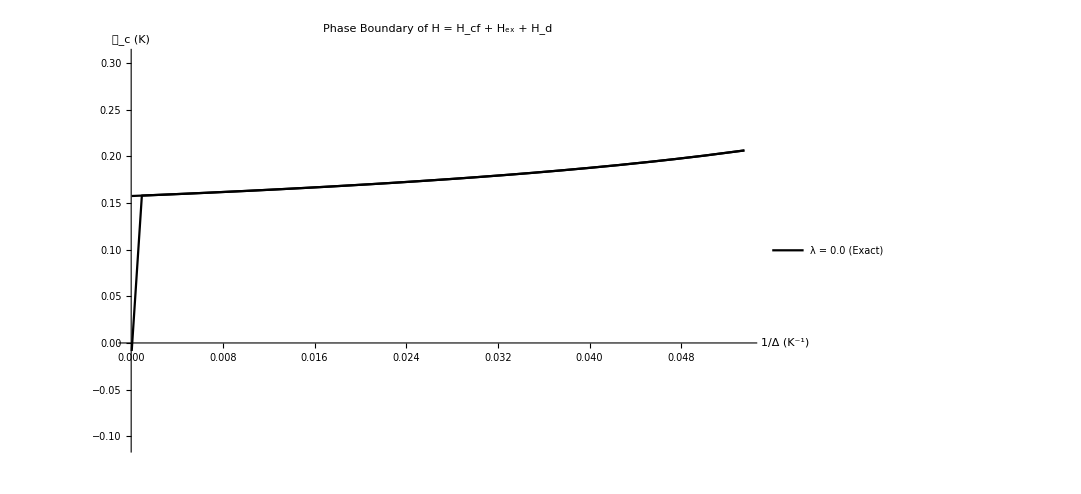

```mathematica
(* Phase boundary plots *)
maxX=Max[InverseΔList];
minY=Min[𝒥cListEff]-0.1;
maxY=Max[𝒥cListEff]+0.1;
dataEff=ConstantArray[0,Length[λList]];
plotEff=ConstantArray[0,Length[λList]];
For[i=1,i≤Length[λList],i++,
dataEff⟦i⟧=Transpose[{InverseΔList,𝒥cListEff⟦i⟧}];
plotEff⟦i⟧=ListPlot[dataEff⟦i⟧,Joined->True,PlotRange->{{0,maxX},{minY,maxY}},PlotStyle->ColorData[3,i],PlotLegends->{"λ = "<>ToString[NumberForm[λList⟦i⟧,{1,1}]]<>" (Exact)"}];
]
data2Eff=ConstantArray[0,Length[λList]];
plot2Eff=ConstantArray[0,Length[λList]];
For[i=1,i≤Length[λList],i++,
data2Eff⟦i⟧=Transpose[{InverseΔList,𝒥c2ListEff⟦i⟧}];
plot2Eff⟦i⟧=ListPlot[data2Eff⟦i⟧,Joined->True,PlotRange->{{0,maxX},{minY,maxY}},PlotStyle->ColorData[3,i]];
]

Show[Flatten[{plotEff,plot2Eff}],PlotLabel->"Phase Boundary of H = H_cf + H_ex + H_d",AxesLabel->{"1/Δ (K^-1)","𝒥_c (K)"},ImageSize->800,LabelStyle->{FontSize->20}]
```

```mathematica
𝒥ListEff
```

{-2.,-1.99,-1.98,-1.97,-1.96,-1.95,-1.94,-1.93,-1.92,-1.91,-1.9,-1.89,-1.88,-1.87,-1.86,-1.85,-1.84,-1.83,-1.82,-1.81,-1.8,-1.79,-1.78,-1.77,-1.76,-1.75,-1.74,-1.73,-1.72,-1.71,-1.7,-1.69,-1.68,-1.67,-1.66,-1.65,-1.64,-1.63,-1.62,-1.61,-1.6,-1.59,-1.58,-1.57,-1.56,-1.55,-1.54,-1.53,-1.52,-1.51,-1.5,-1.49,-1.48,-1.47,-1.46,-1.45,-1.44,-1.43,-1.42,-1.41,-1.4,-1.39,-1.38,-1.37,-1.36,-1.35,-1.34,-1.33,-1.32,-1.31,-1.3,-1.29,-1.28,-1.27,-1.26,-1.25,-1.24,-1.23,-1.22,-1.21,-1.2,-1.19,-1.18,-1.17,-1.16,-1.15,-1.14,-1.13,-1.12,-1.11,-1.1,-1.09,-1.08,-1.07,-1.06,-1.05,-1.04,-1.03,-1.02,-1.01,-1.,-0.99,-0.98,-0.97,-0.96,-0.95,-0.94,-0.93,-0.92,-0.91,-0.9,-0.89,-0.88,-0.87,-0.86,-0.85,-0.84,-0.83,-0.82,-0.81,-0.8,-0.79,-0.78,-0.77,-0.76,-0.75,-0.74,-0.73,-0.72,-0.71,-0.7,-0.69,-0.68,-0.67,-0.66,-0.65,-0.64,-0.63,-0.62,-0.61,-0.6,-0.59,-0.58,-0.57,-0.56,-0.55,-0.54,-0.53,-0.52,-0.51,-0.5,-0.49,-0.48,-0.47,-0.46,-0.45,-0.44,-0.43,-0.42,-0.41,-0.4,-0.39,-0.38,-0.37,-0.36,-0.35,-0.34,-0.33,-0.32,-0.31,-0.3,-0.29,-0.28,-0.27,-0.26,-0.25,-0.24,-0.23,-0.22,-0.21,-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.}

### State Determination

```mathematica
(* Determine which basis state the ground states form *)
```

```mathematica
(* Eigenstates represented in the basis of the two lowest-lying doublets *)
pStateEff={1,0};
mStateEff={0,1};

mmmmEff=Flatten[KroneckerProduct[mStateEff,mStateEff,mStateEff,mStateEff]];

pmmmEff=Flatten[KroneckerProduct[pStateEff,mStateEff,mStateEff,mStateEff]];
mpmmEff=Flatten[KroneckerProduct[mStateEff,pStateEff,mStateEff,mStateEff]];
mmpmEff=Flatten[KroneckerProduct[mStateEff,mStateEff,pStateEff,mStateEff]];
mmmpEff=Flatten[KroneckerProduct[mStateEff,mStateEff,mStateEff,pStateEff]];

ppmmEff=Flatten[KroneckerProduct[pStateEff,pStateEff,mStateEff,mStateEff]];
pmpmEff=Flatten[KroneckerProduct[pStateEff,mStateEff,pStateEff,mStateEff]];
pmmpEff=Flatten[KroneckerProduct[pStateEff,mStateEff,mStateEff,pStateEff]];
mppmEff=Flatten[KroneckerProduct[mStateEff,pStateEff,pStateEff,mStateEff]];
mpmpEff=Flatten[KroneckerProduct[mStateEff,pStateEff,mStateEff,pStateEff]];
mmppEff=Flatten[KroneckerProduct[mStateEff,mStateEff,pStateEff,pStateEff]];

pppmEff=Flatten[KroneckerProduct[pStateEff,pStateEff,pStateEff,mStateEff]];
ppmpEff=Flatten[KroneckerProduct[pStateEff,pStateEff,mStateEff,pStateEff]];
pmppEff=Flatten[KroneckerProduct[pStateEff,mStateEff,pStateEff,pStateEff]];
mpppEff=Flatten[KroneckerProduct[mStateEff,pStateEff,pStateEff,pStateEff]];

ppppEff=Flatten[KroneckerProduct[pStateEff,pStateEff,pStateEff,pStateEff]];

ϵ=Exp[2*π*ⅈ/3]//N;

(* Tetrahedron basis states given by "Quantum spin configurations in Tb_2Ti_2O_7" by Curnoe, doi:10.1103/PhysRevB.75.212404 *)
A1Eff=1/√6*(ppmmEff+pmpmEff+pmmpEff+mppmEff+mpmpEff+mmppEff);
Ep1Eff=ppppEff;
Em1Eff=mmmmEff;
Ep2Eff=1/2*(pmmmEff+mpmmEff+mmpmEff+mmmpEff);
Em2Eff=1/2*(pppmEff+ppmpEff+pmppEff+mpppEff);
Ep3Eff=1/√6*(ppmmEff+ϵ*pmpmEff+ϵ^2*pmmpEff+mmppEff+ϵ*mpmpEff+ϵ^2*mppmEff);
Em3Eff=1/√6*(ppmmEff+ϵ**pmpmEff+ϵ*^2*pmmpEff+mmppEff+ϵ**mpmpEff+ϵ*^2*mppmEff);
T1x1Eff=1/(2*√2)*(-ϵ^2*pppmEff+ϵ^2*ppmpEff+ϵ^2*pmppEff-ϵ^2*mpppEff+ϵ*pmmmEff-ϵ*mpmmEff-ϵ*mmpmEff+ϵ*mmmpEff);
T1y1Eff=1/(2*√2)*(ϵ*pppmEff-ϵ*ppmpEff+ϵ*pmppEff-ϵ*mpppEff+ϵ^2*pmmmEff-ϵ^2*mpmmEff+ϵ^2*mmpmEff-ϵ^2*mmmpEff);
T1z1Eff=1/(2*√2)*(pppmEff+ppmpEff-pmppEff-mpppEff+pmmmEff+mpmmEff-mmpmEff-mmmpEff);
T1x2Eff=1/√2*(pmmpEff-mppmEff);
T1y2Eff=1/√2*(pmpmEff-mpmpEff);
T1z2Eff=1/√2*(ppmmEff-mmppEff);
T2xEff=1/(2*√2)*(-ϵ^2*pppmEff+ϵ^2*ppmpEff+ϵ^2*pmppEff-ϵ^2*mpppEff-ϵ*pmmmEff+ϵ*mpmmEff+ϵ*mmpmEff-ϵ*mmmpEff);
T2yEff=1/(2*√2)*(ϵ*pppmEff-ϵ*ppmpEff+ϵ*pmppEff-ϵ*mpppEff-ϵ^2*pmmmEff+ϵ^2*mpmmEff-ϵ^2*mmpmEff+ϵ^2*mmmpEff);
T2zEff=1/(2*√2)*(pppmEff+ppmpEff-pmppEff-mpppEff-pmmmEff-mpmmEff+mmpmEff+mmmpEff);
```

```mathematica
(* 1/Δ points *)
InverseΔList={0.000046656298600308496,0.0009331259720062202,0.0019595645412130644,0.0033125972006220836,0.004992223950233283,0.0066718506998444775,0.009984447900466563,0.01250388802488336,0.015,0.01665629860031104,0.0175,0.020808709175738727,0.0225,0.025007776049766724,0.0275,0.028506998444790047,0.03,0.0325,0.03331259720062209,0.035,0.0375,0.03998444790046657,0.0425,0.04544323483670297,0.0475,0.05,0.05351477449455676};
ΔList=1./InverseΔList;

(* Critical 𝒥 points signifying the change in ground-state degeneracy (change of phase) *)
λList={0.0};
ΔList={100};
𝒥List=Range[-2,2,0.01];
fidelityListEff=Table[0,{n,16},{i,Length[λList]},{j,Length[ΔList]},{k,Length[𝒥List]}];

For[i=1,i≤Length[λList],i++,
λ=λList⟦i⟧;

For[j=1,j≤Length[ΔList],j++,
Δ=ΔList⟦j⟧;
crystalFieldH=HcfFull[Δ];

For[k=1,k≤Length[𝒥List],k++,
𝒥=𝒥List⟦k⟧;

H=projectedHamiltonian[Δ,𝒥,𝒟,λ*𝒬,states];;
{energies,energyKets}=Transpose[Sort[Transpose[Eigensystem[H]],Re[#1⟦1⟧]<Re[#2⟦1⟧]&]];
energyKets=Chop[energyKets,10^-6];
fidelityListEff⟦1,i,j,k⟧=Norm[energyKets⟦1⟧.A1Eff]//Chop;
fidelityListEff⟦2,i,j,k⟧=Norm[energyKets⟦1⟧.Ep3Eff]//Chop;
fidelityListEff⟦3,i,j,k⟧=Norm[energyKets⟦1⟧.Em3Eff]//Chop;
fidelityListEff⟦4,i,j,k⟧=Norm[energyKets⟦1⟧.T1x2Eff]//Chop;
fidelityListEff⟦5,i,j,k⟧=Norm[energyKets⟦1⟧.T1y2Eff]//Chop;
fidelityListEff⟦6,i,j,k⟧=Norm[energyKets⟦1⟧.T1z2Eff]//Chop;
fidelityListEff⟦7,i,j,k⟧=Norm[energyKets⟦1⟧.Ep1Eff]//Chop;
fidelityListEff⟦8,i,j,k⟧=Norm[energyKets⟦1⟧.Em1Eff]//Chop;
]
]
]
```

### Fidelity Plots

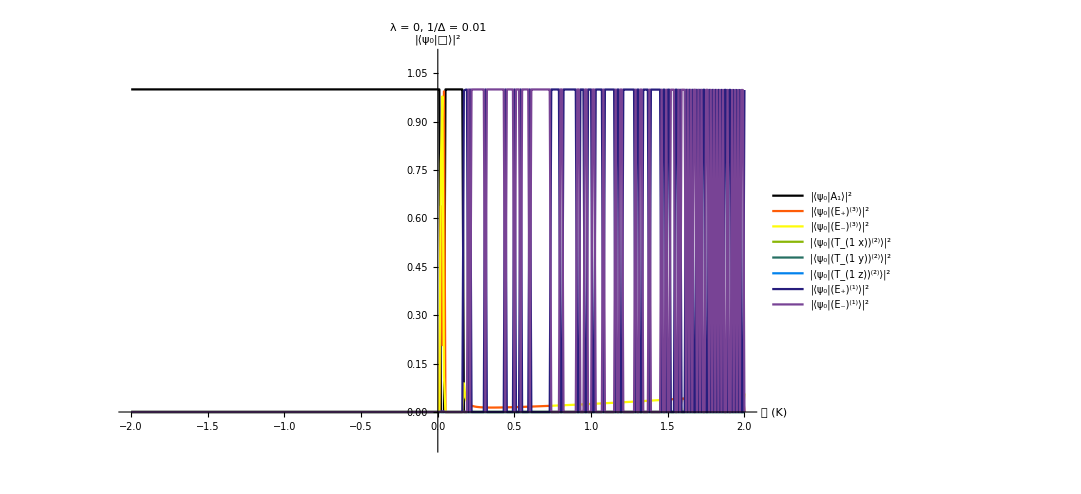

```mathematica
(* Phase boundary plots *)
minX=Min[𝒥List];
maxX=Max[𝒥List];
minY=Min[fidelityListEff]-0.1;
maxY=Max[fidelityListEff]+0.1;
dataEff=ConstantArray[0,8];
plotEff=ConstantArray[0,8];

legend= {"A_1","(E_+)^(3)","(E_-)^(3)","(T_(1  x))^(2)","(T_(1  y))^(2)","(T_(1  z))^(2)","(E_+)^(1)","(E_-)^(1)"};
For[n=1,n≤8,n++,
dataEff⟦n⟧=Transpose[{𝒥List,fidelityListEff⟦n,1,1,All⟧}];
plotEff⟦n⟧=ListPlot[dataEff⟦n⟧,Joined->True,PlotRange->{{minX,maxX},{minY,maxY}},PlotStyle->ColorData[3,n],PlotLegends->{"|⟨ψ_0|"<>legend⟦n⟧<>"⟩|^2"}];
]

Show[plotEff,PlotLabel->"λ = 0, 1/Δ = 0.01",AxesLabel->{"𝒥 (K)","|⟨ψ_0|□⟩|^2"},ImageSize->800,LabelStyle->{FontSize->20}]
```